```mathematica
<<ACPackages`
```

```mathematica
SetWorkDir["2011.10.03\\Re1"]
```

d:\Home\Anton\programs\old\shellgrid(3dp)\2011.10.03\Re1

```mathematica
AverageTimeProfil[l_List,t_,dt_:1]:=Apply[Plus,#]/Length[#]&[Map[#[[2]]&,Select[lv,(t≤#[[1]][[1]]<t+dt)&]]];
```

```mathematica
Off[Thread::tdlen];
lv=ReadList["vv.dat"];lv=Map[Apply[List,#]&,lv];
ltm=Flatten[First/@lv];
{Length[ltm],Last[ltm]}
```

{1908,0.591089}

```mathematica
Manipulate[ListLinePlot[lv⟦i,2⟧,PlotLabel->lv⟦i,1⟧,PlotRange->{0,1}],{i,1,Length[lv],1}]
```

```mathematica
PrintAnim[CutList[#[[2]]&/@lv,20]]
```

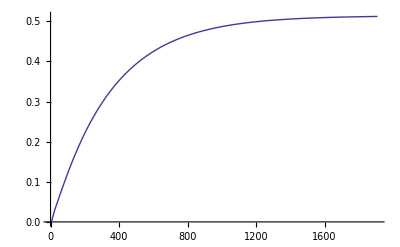

```mathematica
ListLinePlot[(Max[#1⟦2⟧]&)/@lv]
```

```mathematica
ListLimit[(Max[#1⟦2⟧]&)/@lv,ApproximationReport->{LimitPlot}]
```

0.607523

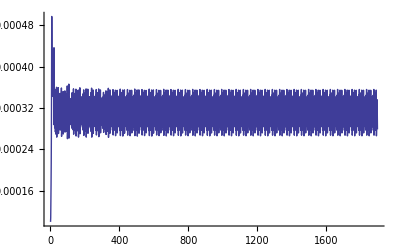

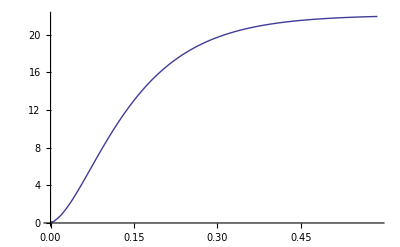

```mathematica
len=Import["energy.dat","Table"];
ltm=First/@len;PrintRange[dif[ltm]]
PrintRange[len]
```

```mathematica
Clue[m_,n_]:=Block[{l=m},
If[n==1,l=Append[Drop[#,-ghost]&/@Drop[l,-1],Last[l]];l=Prepend[Drop[#,ghost]&/@Drop[l,1],First[l]];,
l=Append[Map[Drop[#,-ghost]&,#,{n-1}]&/@Drop[l,-1],Last[l]];
l=Prepend[Map[Drop[#,ghost]&,#,{n-1}]&/@Drop[l,1],First[l]];
(*l1=Map[Drop[#,-ghost]&,#,{n-1}]&;l2=Map[Drop[#,ghost]&,m2,{n-1}];*)];
Return[MapThread[Join,l,n-1]];
];
```

```mathematica
{vx,vy,vz,p,nut}=ReadTextSnapFile["runtest_1000.snp",5];
```

{1,1,1}

{0.310214,1000,20,20,40,1.}

ghost=3

```mathematica
Max[Abs[#]]&/@{vx,vy,vz,p}
```

{0.48672,1.3119×10^-8,9.6214×10^-8,4.2802×10^-6}

```mathematica
ListPlot3D[#,PlotRange->All]&/@vx
```

```mathematica
Union@Flatten@nut
```

{0,1}

```mathematica
ListPlot3D[vx⟦4⟧,PlotRange->All]
```

```mathematica
{vx1,vy1,vz1,p1}={vx,vy,vz,p};
```

```mathematica
{vx2,vy2,vz2,p2}={vx,vy,vz,p};
```

```mathematica
Max/@{vx2-vx1,vy2-vy1,vz2-vz1,p2-p1}
```

{0.10888,0.,0.,0.}

```mathematica
ListPlot3D[#[[5]]&/@vx]
ListPlot3D[#[[5]]&/@vy]
ListPlot3D[#[[5]]&/@vz]
ListPlot3D[#[[5]]&/@p]
```

```mathematica
ListPlot3D[#[[5]]&/@vx1,ViewPoint->{-0.012, -3.220, 1.040}]
ListPlot3D[#[[5]]&/@vx2,ViewPoint->{-0.012, -3.220, 1.040}]
ListPlot3D[#[[5]]&/@(vx2-vx1),ViewPoint->{-0.012, -3.220, 1.040}]
```